# The expected SFS under positive selection Here I examine the expected uSFS under positive selection, based on results from Poisson Random Field theory.

### Neutral SFS Let’s start by examining the SFS expected under neutrality...

```mathematica
NeutSFS[THETA_,i_ ]:=THETA/i
```

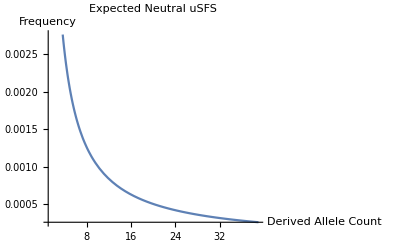

and classic Hartl is of PRF reusult Sawyer the This...

```mathematica
Plot[NeutSFS[0.01,i], {i,1,39},AxesLabel->{"Derived Allele Count","Frequency"},PlotLabel->"Expected Neutral uSFS"]

This is the classic PRF reusult of Sawyer and Hartl...
```

### SFS for positively selected mutations Now let’s look at the uSFS expected under strong positive selection...

```mathematica
SelSFSfixed[S_,pA_,THETA_,i_, n_]:=Module[{H,B},
H[x_] = (1 - Exp[-S*(1-x)]) / (x*(1-x)*(1-Exp[-S]));
B[x_] = Binomial[n,i] * (x^i)*(1-x)^(n-i);
THETA*pA*NIntegrate[B[i,n,x]*H[x],{x,0,1}]]
```

```mathematica
Plot[SelSFSfixed[10,0.01,0.01,i,40], {i,1,39},AxesLabel->{"Derived Allele Count","Frequency"},PlotLabel->"Expected Neutral uSFS"]
```

NIntegrate::inumr: The integrand ((1-ⅇ^(-10 (1-x))) B$571352[1.00078,40,x])/((1-1/ⅇ^10) (1-x) x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
SelSFSpoint[S_,pA_,THETA_,i_, n_]:=Module[{H,B},
H[k_] = (1 - Exp[-S*(1-k)]) / (k*(1-k)*(1-Exp[-S]));
B[i, n, p_] = Binomial[n,i] * (p^i)*(1-p)^(n-i);
THETA*NIntegrate[B[i,n,x]*H[x],{x,0.001,0.999}]]
```

```mathematica
SelSFSpoint[100,0.001,0.01,1,40]
```

0.00986392

```mathematica
H[S_,x_] = (1 - Exp[-S*(1-x)]) / (x*(1-x)*(1-Exp[-S]));

B[r_,n_,x_] = Binomial[n,r] * (x^r)*(1-x)^(n-r);

0.01*0.001*Integrate[H[100,x]*B[1,40,x],{x,0,1}]
```

0.0000102564

```mathematica
Plot[(0.01 *0.001* Integrate[H[1000,x]*B[i,40,x],{x,0,1}]),{i,1,2}]
```

$Aborted

```mathematica
SFS = Table[ { 100,0.001,i, 0.01*0.001*Integrate[H[100,x]*B[i,40,x],{x,0,1}]},  {i, 1,2}] ;

SFS
```

{{100,0.001,1,0.0000102564},{100,0.001,2,5.26316×10^-6}}

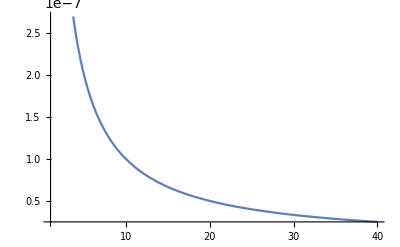

```mathematica
Plot[ 0.01*0.0001*NIntegrate[H[0.0001,x]*B[i,40,x], {x,0,1}], {i,1,40}]
```

```mathematica
headers={"S","pA","i","SFS_i"};

SFS1000pA0001 = Table[ { 1000,0.0001,i, 0.01*0.0001*NIntegrate[H[1000,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS500pA0001 = Table[ { 500,0.0001,i, 0.01*0.0001*NIntegrate[H[500,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS100pA0001 = Table[ { 100,0.001,i, 0.01*0.001*NIntegrate[H[100,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS10pA0001 = Table[ { 10,0.01,i, 0.01*0.01*NIntegrate[H[10,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;

SFS0pA0001= Table[ { 0,0.0,i, 0.01*0.01*NIntegrate[H[0.00001,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
```

```mathematica
data1000pA0001=Prepend[SFS1000pA0001,headers];
data500pA0001=Prepend[SFS500,headers];
data100pA0001=Prepend[SFS100,headers];
data10pA0001=Prepend[SFS10,headers];
data0pA0001=Prepend[SFS0,headers];
```

```mathematica
data1000
```

```mathematica
Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS1000pA0001.csv",data1000pA0001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS500pA0001.csv",data500pA0001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS100pA0001.csv",data100pA0001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS10pA0001.csv",data10pA0001];
Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS0pA0001.csv",data0pA0001];
```

```mathematica
headers={"S","pA","i","SFS_i"};

SFS1000pA0001 = Table[ { 1000,0.0001,i, 0.01*0.0001*NIntegrate[H[1000,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS500pA0001 = Table[ { 500,0.0001,i, 0.01*0.0001*NIntegrate[H[500,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS100pA0001 = Table[ { 100,0.0001,i, 0.01*0.0001*NIntegrate[H[100,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS50pA0001 = Table[ { 50,0.0001,i, 0.01*0.0001*NIntegrate[H[50,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS10pA0001 = Table[ { 10,0.0001,i, 0.01*0.0001*NIntegrate[H[10,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS0pA0001 = Table[ { 0.0,0.0001,i, 0.01*0.0001*NIntegrate[H[0.0001,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;

data1000pA0001=Prepend[SFS1000pA0001,headers];
data500pA0001=Prepend[SFS500pA0001,headers];
data100pA0001=Prepend[SFS100pA0001,headers];
data50pA0001=Prepend[SFS50pA0001,headers];
data10pA0001=Prepend[SFS10pA0001,headers];
data0pA0001=Prepend[SFS0pA0001,headers];

Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS1000pA0001.csv",data1000pA0001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS500pA0001.csv",data500pA0001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS100pA0001.csv",data100pA0001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS50pA0001.csv",data50pA0001];
Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS10pA0001.csv",data10pA0001];
Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS0pA0001.csv",data0pA0001];

SFS1000pA001 = Table[ { 1000,0.001,i, 0.01*0.001*NIntegrate[H[1000,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS500pA001 = Table[ { 500,0.001,i, 0.01*0.001*NIntegrate[H[500,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS100pA001 = Table[ { 100,0.001,i, 0.01*0.001*NIntegrate[H[100,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS50pA001 = Table[ { 50,0.001,i, 0.01*0.001*NIntegrate[H[50,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS10pA001 = Table[ { 10,0.001,i, 0.01*0.001*NIntegrate[H[10,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS0pA001 = Table[ { 0.0,0.001,i, 0.01*0.001*NIntegrate[H[0.0001,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;

data1000pA001=Prepend[SFS1000pA001,headers];
data500pA001=Prepend[SFS500pA001,headers];
data100pA001=Prepend[SFS100pA001,headers];
data50pA001=Prepend[SFS50pA001,headers];
data10pA001=Prepend[SFS10pA001,headers];
data0pA001=Prepend[SFS0pA001,headers];

Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS1000pA001.csv",data1000pA001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS500pA001.csv",data500pA001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS100pA001.csv",data100pA001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS50pA001.csv",data50pA001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS10pA001.csv",data10pA001];
Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS0pA001.csv",data0pA001];

SFS1000pA01 = Table[ { 1000,0.01,i, 0.01*0.01*NIntegrate[H[1000,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS500pA01 = Table[ { 500,0.01,i, 0.01*0.01*NIntegrate[H[500,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS100pA01 = Table[ { 100,0.01,i, 0.01*0.01*NIntegrate[H[100,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS50pA01 = Table[ { 50,0.01,i, 0.01*0.01*NIntegrate[H[50,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS10pA01 = Table[ { 10,0.01,i, 0.01*0.01*NIntegrate[H[10,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS0pA01 = Table[ { 0.0,0.01,i, 0.01*0.01*NIntegrate[H[0.0001,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;

data1000pA01=Prepend[SFS1000pA01,headers];
data500pA01=Prepend[SFS500pA01,headers];
data100pA01=Prepend[SFS100pA01,headers];
data50pA01=Prepend[SFS50pA01,headers];data10pA01=Prepend[SFS10pA01,headers];
data0pA01=Prepend[SFS0pA01,headers];

Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS1000pA01.csv",data1000pA01];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS500pA01.csv",data500pA01];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS100pA01.csv",data100pA01];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS50pA01.csv",data50pA01];
Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS10pA01.csv",data10pA01];
Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS0pA01.csv",data0pA01];
```

```mathematica
headers={"S","pA","i","SFS_i"};

SFS1000pA0001 = Table[ { 1000,0.0001,i, 0.01*0.0001*NIntegrate[H[1000,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS500pA0001 = Table[ { 500,0.0001,i, 0.01*0.0001*NIntegrate[H[500,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS100pA0001 = Table[ { 100,0.0001,i, 0.01*0.0001*NIntegrate[H[100,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS50pA0001 = Table[ { 50,0.0001,i, 0.01*0.0001*NIntegrate[H[50,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS10pA0001 = Table[ { 10,0.0001,i, 0.01*0.0001*NIntegrate[H[10,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS0pA0001 = Table[ { 0.0,0.0001,i, 0.01*0.0001*NIntegrate[H[0.0001,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;

data1000pA0001=Prepend[SFS1000pA0001,headers];
data500pA0001=Prepend[SFS500pA0001,headers];
data100pA0001=Prepend[SFS100pA0001,headers];
data50pA0001=Prepend[SFS50pA0001,headers];
data10pA0001=Prepend[SFS10pA0001,headers];
data0pA0001=Prepend[SFS0pA0001,headers];

Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS1000pA0001.csv",data1000pA0001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS500pA0001.csv",data500pA0001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS100pA0001.csv",data100pA0001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS10pA0001.csv",data10pA0001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS50pA0001.csv",data50pA0001];
Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS0pA0001.csv",data0pA0001];

SFS1000pA001 = Table[ { 1000,0.001,i, 0.01*0.001*NIntegrate[H[1000,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS500pA001 = Table[ { 500,0.001,i, 0.01*0.001*NIntegrate[H[500,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS100pA001 = Table[ { 100,0.001,i, 0.01*0.001*NIntegrate[H[100,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS50pA001 = Table[ { 50,0.001,i, 0.01*0.001*NIntegrate[H[50,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS10pA001 = Table[ { 10,0.001,i, 0.01*0.001*NIntegrate[H[10,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS0pA001 = Table[ { 0.0,0.001,i, 0.01*0.001*NIntegrate[H[0.0001,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;

data1000pA001=Prepend[SFS1000pA001,headers];
data500pA001=Prepend[SFS500pA001,headers];
data100pA001=Prepend[SFS100pA001,headers];
data50pA001=Prepend[SFS50pA001,headers];
data10pA001=Prepend[SFS10pA001,headers];
data0pA001=Prepend[SFS0pA001,headers];

Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS1000pA001.csv",data1000pA001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS500pA001.csv",data500pA001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS100pA001.csv",data100pA001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS50pA001.csv",data50pA001];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS10pA001.csv",data10pA001];
Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS0pA001.csv",data0pA001];

SFS1000pA01 = Table[ { 1000,0.01,i, 0.01*0.01*NIntegrate[H[1000,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS500pA01 = Table[ { 500,0.01,i, 0.01*0.01*NIntegrate[H[500,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS100pA01 = Table[ { 100,0.01,i, 0.01*0.01*NIntegrate[H[100,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS50pA01 = Table[ { 50,0.01,i, 0.01*0.01*NIntegrate[H[50,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS10pA01 = Table[ { 10,0.01,i, 0.01*0.01*NIntegrate[H[10,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;
SFS0pA01 = Table[ { 0.0,0.01,i, 0.01*0.01*NIntegrate[H[0.0001,x]*B[i,400,x],{x,0,1}]},  {i, 1,399}] ;

data1000pA01=Prepend[SFS1000pA01,headers];
data500pA01=Prepend[SFS500pA01,headers];
data100pA01=Prepend[SFS100pA01,headers];
data10pA01=Prepend[SFS10pA01,headers];data50pA01=Prepend[SFS50pA01,headers];
data0pA01=Prepend[SFS0pA01,headers];

Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS1000pA01.csv",data1000pA01];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS500pA01.csv",data500pA01];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS100pA01.csv",data100pA01];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS50pA01.csv",data50pA01];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS10pA01.csv",data10pA01];
Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/n400_SFS0pA01.csv",data0pA01];
```